```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\neurobayes\\overtraining\\code\\"]
```

C:\Users\pglpm\repositories\neurobayes\overtraining\code

```mathematica
(* coordinate transformations: map the normalized triplet of frequencies to a 2D simplex in R^2 *)
```

```mathematica
trmatrix=T[{{1,0},{0,0},{1/2,Sqrt[3]/2}}];proj[p_]:=trmatrix.p;

(* This is the representation of the simplex as a triangle *)

sp1={Black,Thin,Line[T[trmatrix][[{1,2,3,1}]]]};
simplex=Graphics[{sp1}];

(* These functions plot normalized triplets of frequencies as points in the 2D simplex. First: as points; second: as empty circles *)

plotfreqspoints[freqs_,colour_:blue]:=Graphics[{{PointSize@Large,Opacity[0.75],colour,Point[proj@freqs]}}];
plotfreqscircles[freqs_,colour_:red]:=Graphics[{{Thick,Opacity[0.75],colour,Circle[proj@freqs,0.02]}}];
plotfreqslines[freqs_,colour_:blue]:=
Graphics[{{Thin,Opacity[0.75],colour,Line[proj/@freqs]}}];
```

```mathematica
(* Illustrations of how predictions via an exchangeable model gets updated with new observations *)
```

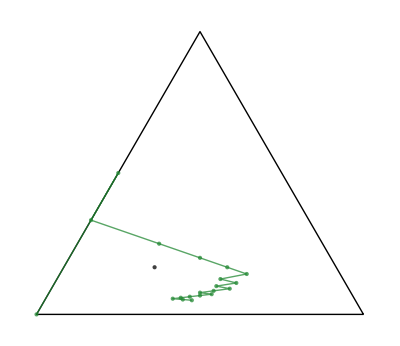

```mathematica
(* Choose a limit frequency *)
limitfreqs=Flatten@{{{1/3,2/3}*25/30,5/30}};

(* Generate outcomes, corresponding to the values 1,2,3 *)
SeedRandom[672];
samples=20;
data=RandomChoice[limitfreqs->Range[3],samples];

datafreqs=Table[(#/Total@#)&@(Count[data[[;;i]],#]&/@{1,2,3}),{i,samples}];

(* Calculate the empirical frequencies from the data *)
finaldatafreqs=Last@datafreqs;

(* Plot the limit and empirical frequencies *)

Show[{simplex,plotfreqslines[datafreqs,green],plotfreqspoints[#,green]&/@datafreqs,plotfreqspoints[limitfreqs,Black]},PlotRange->All]
```

```mathematica
prior[f1_,f2_,a1_,a2_,a3_]=Assuming[a1>0&&a2>0&&a3>0,FS[PDF[DirichletDistribution[{a1,a2,a3}],{f1,f2}]]]
```

Piecewise[{{(f1^(-1+a1) (1-f1-f2)^(-1+a3) f2^(-1+a2) Gamma[a1+a2+a3])/(Gamma[a1] Gamma[a2] Gamma[a3]), f1>0&&f2>0&&f1+f2<1}, {0, True}}]

```mathematica
predictiveprob[a1_,a2_,a3_]=Assuming[a1>0&&a2>0&&a3>0,FS[Integrate[{f1,f2,1-f1-f2}*prior[f1,f2,a1,a2,a3],{f1,0,1},{f2,0,1},Assumptions->a1>0&&a2>0&&a3>0]]]
```

{a1/(a1+a2+a3),a2/(a1+a2+a3),a3/(a1+a2+a3)}

```mathematica
RandomVariate[DirichletDistribution[initialparameters],4]
```

{{0.0299241,0.885814},{0.994947,0.00505138},{0.631871,0.367784},{1.90755×10^-14,0.987491}}

```mathematica
initialparameters={0.1,0.1,0.1};
```

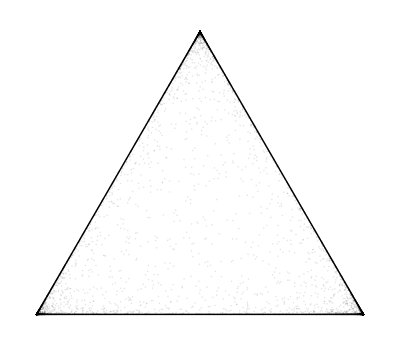

```mathematica
Show[{simplex,ListPlot[proj[Flatten@{#,1-Total@#}]&/@RandomVariate[DirichletDistribution[initialparameters],10000],PlotStyle->{Black,Opacity[0.1]}]}]
```

```mathematica
ProgressIndicator[Dynamic[i],{0,Length@data}]
```

```mathematica
updatepoints=Join[{observedfreqs=Table[0,3];
oldjointprob=1;
newjointprob=predictiveprob[Sequence@@initialparameters]}
,
Table[
predictiveprob[Sequence@@(
initialparameters+datafreqs[[i]]*i
)]
,{i,Length@data}]];
```

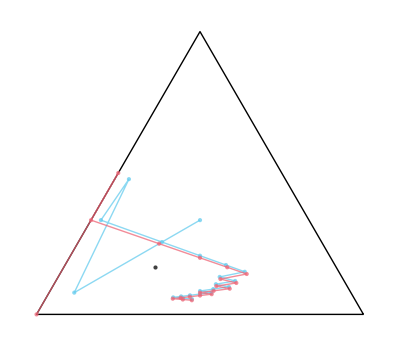

```mathematica
Show[{simplex,plotfreqspoints[limitfreqs,Black],plotfreqslines[updatepoints,blue],plotfreqspoints[#,blue]&/@updatepoints,plotfreqslines[datafreqs,red],plotfreqspoints[#,red]&/@datafreqs},PlotRange->All]
```

```mathematica
initialparameters={10,10,10};
```

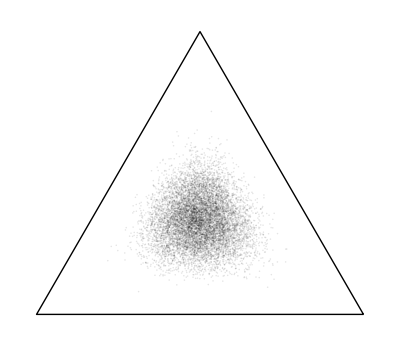

```mathematica
Show[{simplex,ListPlot[proj[Flatten@{#,1-Total@#}]&/@RandomVariate[DirichletDistribution[initialparameters],10000],PlotStyle->{Black,Opacity[0.1]}]}]
```

```mathematica
updatepoints2=Join[{observedfreqs=Table[0,3];
oldjointprob=1;
newjointprob=predictiveprob[Sequence@@initialparameters]}
,
Table[
predictiveprob[Sequence@@(
initialparameters+datafreqs[[i]]*i
)]
,{i,Length@data}]];
```

```mathematica
Show[{simplex,plotfreqslines[updatepoints2,blue],plotfreqspoints[#,blue]&/@updatepoints2,plotfreqslines[datafreqs,red],plotfreqspoints[#,red]&/@datafreqs,plotfreqspoints[limitfreqs,Black]},PlotRange->All]
```

-Graphics-

```mathematica
initialparameters={1,1,1};
```

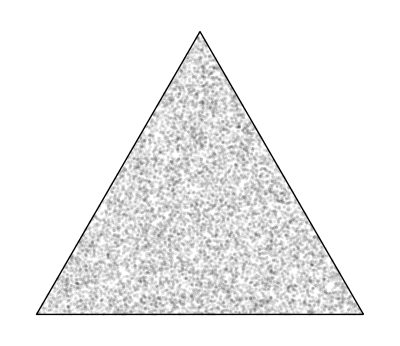

```mathematica
Show[{simplex,ListPlot[proj[Flatten@{#,1-Total@#}]&/@RandomVariate[DirichletDistribution[initialparameters],10000],PlotStyle->{Black,Opacity[0.1]}]}]
```

```mathematica
updatepoints3=Join[{observedfreqs=Table[0,3];
oldjointprob=1;
newjointprob=predictiveprob[Sequence@@initialparameters]}
,
Table[
predictiveprob[Sequence@@(
initialparameters+datafreqs[[i]]*i
)]
,{i,Length@data}]];
```

```mathematica
Show[{simplex,plotfreqslines[updatepoints3,blue],plotfreqspoints[#,blue]&/@updatepoints3,plotfreqslines[datafreqs,red],plotfreqspoints[#,red]&/@datafreqs,plotfreqspoints[limitfreqs,Black]},PlotRange->All]
```

-Graphics-

```mathematica
parameters={1/10,1/10,1/10};prior[f1_,f2_]=PDF[DirichletDistribution[parameters],{f1,f2}];
Integrate[{f1,f2,1-f1-f2}*prior[f1,f2],{f1,0,1},{f2,0,1}]
```

{1/3,1/3,1/3}

```mathematica
updatepoints2=Join[{observedfreqs=Table[0,3];
oldjointprob=1;
newjointprob=Integrate[{f1,f2,1-f1-f2}*prior[f1,f2],{f1,0,1},{f2,0,1}]}
,
Table[
oldjointprob=newjointprob[[data[[i]]]];

newjointprob=Integrate[{f1,f2,1-f1-f2}*Times@@({f1,f2,1-f1-f2}^observedfreqs)*prior[f1,f2],{f1,0,1},{f2,0,1}(*,AccuracyGoal->+Infinity,PrecisionGoal->3*)];

newjointprob/oldjointprob
,{i,Length@data}]];
```

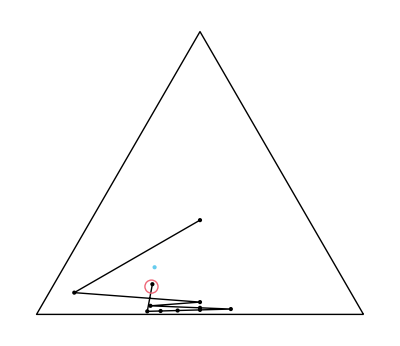

```mathematica
Show[{simplex,plotfreqslines@updatepoints2,plotfreqspoints2/@updatepoints2,plotfreqspoints@limitfreqs,plotfreqscircles@datafreqs},PlotRange->All]
```

```mathematica
rfreqs=Flatten@{{{1/2,1/2}*25/30,5/30}};
samples=20;
reps=250;
m=5;s=1;
pprob=Table[0,{samples},{3}];
lnpprob=Table[0,{samples},{3}];
pred=Table[0,{samples}];
surpr=Table[0,{samples}];
logev=Table[0,{samples}];
efreq=Table[0,{3}];

Do[
data=RandomChoice[rfreqs->Range[3],samples];

freqs=Table[0,{3}];
evidence=1;
(*probh=Table[Null,{samples}];*)

Do[(*Print[i];Print[freqs];*)
integral=
NIntegrate[prob[t]*Times@@(prob[t]^freqs)*priort[t,m,s],{t,-Infinity,+Infinity}];
(*Print[{i,integral//MF}];*)
probh=integral/evidence;
pprob[[i]]+=probh;
lnpprob[[i]]+=Log[probh];
(*Print[integral];Print[probh[[i]]];Print[data[[i]]];*)

datum=data[[i]];
pred[[i]]+=probh[[datum]];
surpr[[i]]+=-Log[probh[[datum]]];

evidence=integral[[datum]];
logev[[i]]+=Log[evidence];
++freqs[[datum]];
,{i,samples}];
efreq+=freqs
,{reps}];

pred=pred/reps;surpr=surpr/reps;logev=logev/reps;
pprob=pprob/reps;lnpprob=lnpprob/reps;efreq=efreq/reps;
```

```mathematica
plotdatafreqs=ParametricPlot[proj@prob[t],{t,-100,100},Axes->None,PlotRange->All,AspectRatio->Auto,PlotStyle->{Thick,purpleblue}];
```

```mathematica
(* algorithm to predict & update from data *)
```

```mathematica
(* parametric model *)
expsum[t_]=Table[(1+0*KroneckerDelta[s,1])*Exp[t*s],{s,{0,2,1}}];
z[t_]=Total@expsum[t];
prob[t_]=Simplify[expsum[t]/z[t]]
```

{1/(1+ⅇ^t+ⅇ^(2 t)),ⅇ^(2 t)/(1+ⅇ^t+ⅇ^(2 t)),ⅇ^t/(1+ⅇ^t+ⅇ^(2 t))}

```mathematica
Integrate[1/Sqrt[Times@@prob[t]],{t,-100,100}]
```

∫_-100^100 1/(√(ⅇ^(3 t)/((1+ⅇ^t+ⅇ^(2 t))^3)))ⅆt

```mathematica
jp[t_]=FS[prob[t].(FS@D[Log@prob[t],t]^2)]/2
```

(2+Cosh[t])/(1+2 Cosh[t])^2

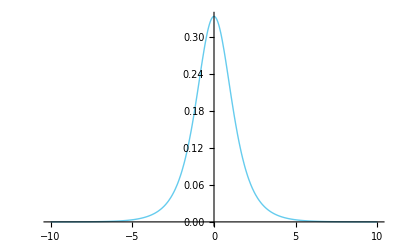

```mathematica
Plot[%,{t,-10,10}]
```

```mathematica
tf[fr_]=Assuming[0<fr<1,FS[t/.Solve[prob[t][[1]]==fr,t,Reals][[1]]]]
```

Log[1/2 (-1+√(-3+4/fr))]

```mathematica
FS[prob[tf[fr]].(FS@D[Log@prob[tf[fr]],fr]^2)]
```

(7+√((4-3 fr)/fr)-6 fr)/(8 fr-14 fr^2+6 fr^3)

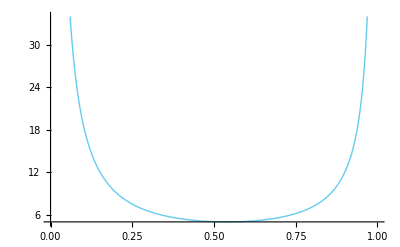

```mathematica
Plot[%,{fr,0,1}]
```

```mathematica
priort[t_,m_,s_]:=(PDF[NormalDistribution[m,s],t]+PDF[NormalDistribution[-m,s],t])/2;
```

```mathematica
priort[t_,m_,s_]:=(PDF[NormalDistribution[m,s],t]);
```

```mathematica
(* representation of parameter density on simplex *)
```

```mathematica
tran[t_]=FS[prob[t][[3]]]
```

1/(1+2 Cosh[t])

```mathematica
somax=prob[0][[3]]
```

1/3

```mathematica
dpdt[t_]=Assuming[Element[t,Reals],FullSimplify[Abs@D[tran[t],t]]]
```

(2 Abs[Sinh[t]])/(1+2 Cosh[t])^2

```mathematica
inve[so_]=t/.Flatten[Assuming[0<so<somax,FS@Solve[so==tran[t],t,Reals]]]
```

-ArcCosh[1/2 (-1+1/so)]

```mathematica
Plot[inve[so],{so,0,somax}]
```

```mathematica
dens[so_]=2*Assuming[0<so<somax,Simplify@jp[inve[so]]/dpdt[inve[so]]]
```

(1+3 so)/(2 so Abs[√((-1+1/2 (-1+1/so))/(1+1/2 (-1+1/so))) (1+1/2 (-1+1/so))])

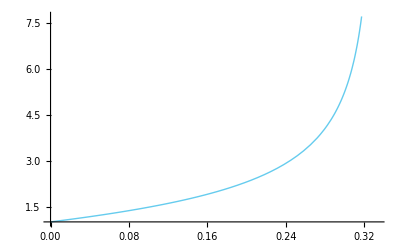

```mathematica
Plot[dens[so],{so,0,somax},PlotRange->Auto]
```

```mathematica
Limit[dens[so,6,1/2],so->somax]
```

∞

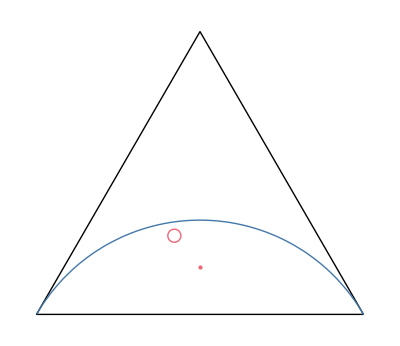

```mathematica
rfreqs=Flatten@{{{1/2,1/2}*25/30,5/30}};

samples=25;
data=RandomChoice[rfreqs->Range[3],samples];

rfreqs0=(#/Total@#)&@(Count[data,#]&/@{1,2,3});


ppplot1=ParametricPlot[proj@prob[t],{t,-100,100},Axes->None,PlotRange->All,AspectRatio->Auto,PlotStyle->{Thick,purpleblue}];
ddoms={Graphics[{sp1}],ppplot1};
Show[{ddoms,plotfreqs@rfreqs,plotcfreqs@rfreqs0},PlotRange->All]
```

```mathematica
ProgressIndicator[Dynamic[i],{0,samples}]
```

```mathematica
rfreqs=Flatten@{{{1/2,1/2}*25/30,5/30}};
samples=20;
reps=250;
m=5;s=1;
pprob=Table[0,{samples},{3}];
lnpprob=Table[0,{samples},{3}];
pred=Table[0,{samples}];
surpr=Table[0,{samples}];
logev=Table[0,{samples}];
efreq=Table[0,{3}];

Do[
data=RandomChoice[rfreqs->Range[3],samples];

freqs=Table[0,{3}];
evidence=1;
(*probh=Table[Null,{samples}];*)

Do[(*Print[i];Print[freqs];*)
integral=
NIntegrate[prob[t]*Times@@(prob[t]^freqs)*priort[t,m,s],{t,-Infinity,+Infinity}];
(*Print[{i,integral//MF}];*)
probh=integral/evidence;
pprob[[i]]+=probh;
lnpprob[[i]]+=Log[probh];
(*Print[integral];Print[probh[[i]]];Print[data[[i]]];*)

datum=data[[i]];
pred[[i]]+=probh[[datum]];
surpr[[i]]+=-Log[probh[[datum]]];

evidence=integral[[datum]];
logev[[i]]+=Log[evidence];
++freqs[[datum]];
,{i,samples}];
efreq+=freqs
,{reps}];

pred=pred/reps;surpr=surpr/reps;logev=logev/reps;
pprob=pprob/reps;lnpprob=lnpprob/reps;efreq=efreq/reps;
```

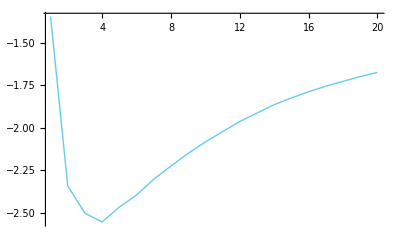

```mathematica
ListPlot[logev/Range[samples],Joined->True,PlotRange->All]
```

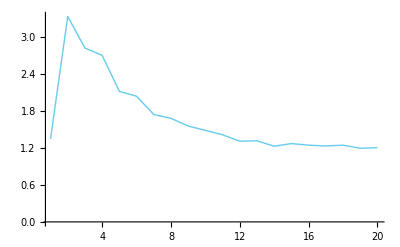

```mathematica
ListPlot[surpr,Joined->True,PlotRange->All]
```

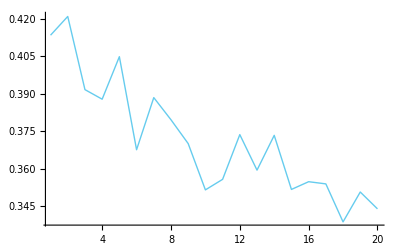

```mathematica
ListPlot[pred,Joined->True,PlotRange->All]
```

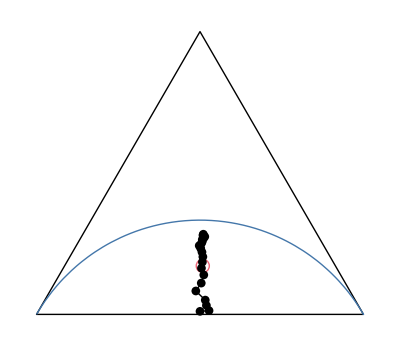

```mathematica
subrange=Round[Range[1,samples,samples/samples]];rplot1=ListPlot[Table[proj@pprob[[i]],{i,subrange}],Axes->None,PlotRange->All,PlotStyle->Black,Joined->True,PlotMarkers->Auto];
Show[{ddoms,plotfreqs@rfreqs,plotcfreqs@efreq,rplot1},PlotRange->All]
```

```mathematica
expng["update_avg"]
```

update_avg.png

```mathematica
entropy[p_]:=Block[{xlogx},
xlogx[x_]:=If[x>0,x*Log[x],0];
SetAttributes[xlogx,Listable];
Total@xlogx[p]];
```

```mathematica
(Exp@-entropy[rfreqs])^10*2//N
```

100218.

```mathematica
Log[Exp@-entropy[rfreqs],100000]//N
```

10.6385

```mathematica
rfreqs
```

{3/8,3/8,1/4}